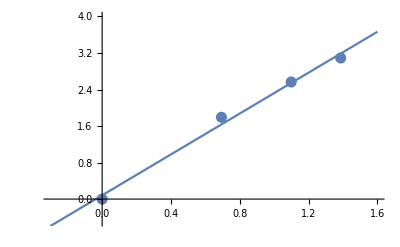

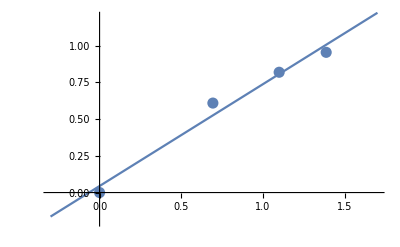

```mathematica
t1=Log[{{1,1},{2,6},{3,13},{4,22}}];
line1=Fit[t1,{1,x},x];
Show[ListPlot[t1,PlotStyle->PointSize[0.02],PlotRange->{{-0.3,1.6},{-0.5,4}}],Plot[line1,{x,-0.3,1.6}]]
t2=Log[{{1,1},{2,1.84},{3,2.27},{4,2.60}}];
line2=Fit[t2,{1,x},x];
Show[ListPlot[t2,PlotStyle->PointSize[0.02],PlotRange->{{-0.3,1.7},{-0.2,1.2}}],Plot[line2,{x,-0.3,1.7}]]
```